```mathematica
{crowntransforms1,lens1,splanes1}={{BracketingBar[-5.5556+0.0000 I,0.0000+-1.0000 I],DoubleBracketingBar[-1.6718+-1.1787 I,0.7012+0.7130 I],DoubleBracketingBar[2.1507+1.2823 I,0.3983+-0.9173 I],DoubleBracketingBar[-0.7306+1.6070 I,0.9948+-0.1014 I],BracketingBar[2.0711+0.4142 I,0.9711+-0.2386 I],DoubleBracketingBar[1.2911+0.6625 I,0.8347+-0.5506 I],BracketingBar[0.6679+-1.8479 I,0.4125+-0.9109 I],BracketingBar[-0.8163+-1.4344 I,0.3202+-0.9473 I]},{2,3,3,3,2,3,2,2},{{{{0.0000,1.0000,0.0000,-0.0000},2},{{0.0000,-5.5556,0.0000,5.4648},1}},{{{1.0000,0.0000,0.0000,-0.0000},2},{{0.7130,0.7012,0.0000,-0.0000},2},{{-2.0126,0.3656,0.0000,1.7844},1}},{{{1.0000,0.0000,0.0000,-0.0000},2},{{-0.9173,0.3983,0.0000,0.0000},2},{{-0.3196,2.4835,0.0000,2.2956},1}},{{{1.0000,0.0000,0.0000,0.0000},2},{{-0.1014,0.9948,0.0000,0.0000},2},{{-0.8898,1.5246,0.0000,1.4547},1}},{{{0.9711,0.2386,0.0000,-0.0000},2},{{1.9125,0.8963,0.0000,1.8603},1}},{{{1.0000,0.0000,0.0000,-0.0000},2},{{-0.5506,0.8347,0.0000,0.0000},2},{{0.7129,1.2640,0.0000,1.0516},1}},{{{0.4125,0.9109,0.0000,0.0000},2},{{1.9589,-0.1539,0.0000,1.6914},1}},{{{0.3202,0.9473,0.0000,0.0000},2},{{1.0975,-1.2326,0.0000,1.3129},1}}}};
```

```mathematica
Graphics[{Inset[mm,Center,Center,2],Circle[{0,0},1],Disk[Comp2Real[0∘#],.012]&/@crowntransforms}]
```

-Graphics-

```mathematica
mm = Import["/Users/strauss/Desktop/Screen Shot 2025-05-03 at 11.47.00 AM.png"];
```

```mathematica
{crowntransforms2,lens2,splanes2}={{BracketingBar[-5.5556+0.0000 I,0.0000+-1.0000 I],DoubleBracketingBar[-1.6718+-1.1787 I,0.7012+0.7130 I],DoubleBracketingBar[2.1507+1.2823 I,0.3983+-0.9173 I],DoubleBracketingBar[-0.7306+1.6070 I,0.9948+-0.1014 I],BracketingBar[2.0711+0.4142 I,0.9711+-0.2386 I],BracketingBar[0.6679+-1.8479 I,0.4125+-0.9109 I],BracketingBar[-0.8163+-1.4344 I,0.3202+-0.9473 I]},{2,3,3,3,2,2,2},{{{{0.0000,1.0000,0.0000,-0.0000},2},{{0.0000,-5.5556,0.0000,5.4648},1}},{{{1.0000,0.0000,0.0000,-0.0000},2},{{0.7130,0.7012,0.0000,-0.0000},2},{{-2.0126,0.3656,0.0000,1.7844},1}},{{{1.0000,0.0000,0.0000,-0.0000},2},{{-0.9173,0.3983,0.0000,0.0000},2},{{-0.3196,2.4835,0.0000,2.2956},1}},{{{1.0000,0.0000,0.0000,0.0000},2},{{-0.1014,0.9948,0.0000,0.0000},2},{{-0.8898,1.5246,0.0000,1.4547},1}},{{{0.9711,0.2386,0.0000,-0.0000},2},{{1.9125,0.8963,0.0000,1.8603},1}},{{{0.4125,0.9109,0.0000,0.0000},2},{{1.9589,-0.1539,0.0000,1.6914},1}},{{{0.3202,0.9473,0.0000,0.0000},2},{{1.0975,-1.2326,0.0000,1.3129},1}}}};
```

```mathematica
mm2 = Import["/Users/strauss/Desktop/Screen Shot 2025-05-03 at 12.24.09 PM.png"];
```

```mathematica
Graphics[{Inset[mm2,Center,Center,2],Circle[{0,0},1],Disk[Comp2Real[0∘#],.012]&/@crowntransforms2}]
```

-Graphics-

```mathematica
ss=Complement[crowntransforms1,crowntransforms2]
ss=ss[[1]]
#∘ss&/@{-.2+-.2I,.2+.2I}
Position[crowntransforms1,ss]
```

{‖1.2911+0.6625 ⅈ,0.8347-0.5506 ⅈ‖}

‖1.2911+0.6625 ⅈ,0.8347-0.5506 ⅈ‖

{0.171838+0.601608 ⅈ,0.463972+0.638621 ⅈ}

{{6}}

```mathematica
splanes1[[6]]
```

{{{1.,0.,0.,0.},2},{{-0.5506,0.8347,0.,0.},2},{{0.7129,1.264,0.,1.0516},1}}

```mathematica
Position[splanes1,{{1.,0.,0.,0.},2}]
```

{{2,1},{3,1},{4,1},{6,1}}

#### Another version, no rotating or shifting, just scaling:

```mathematica
{crowntransforms1,lens1,splanes1}={{BracketingBar[-0.4862+1.7453 I,-0.5047+-0.8633 I],BracketingBar[1.7149+0.8043 I,-0.9970+-0.0773 I],BracketingBar[1.7149+-0.8043 I,-0.9970+-0.0773 I],BracketingBar[0.0000+1.0000 I,0.0000+0.0000 I],BracketingBar[3.1559+0.0000 I,0.2265+-0.9740 I],DoubleBracketingBar[0.9349+-1.5991 I,0.9007+0.4344 I],DoubleBracketingBar[0.9349+-1.5991 I,0.9007+-0.4344 I],BracketingBar[0.7848+-1.2378 I,-0.2769+-0.9609 I],BracketingBar[-0.4862+-1.7453 I,-0.5047+-0.8633 I]},{2,2,2,2,2,3,3,2,2},{{{{-0.5047,0.8633,0.0000,-0.0000},2},{{-1.2612,-1.3006,0.0000,1.5108},1}},{{{-0.9970,0.0773,0.0000,0.0000},2},{{-1.7719,-0.6694,0.0000,1.6087},1}},{{{-0.9970,0.0773,0.0000,-0.0000},2},{{-1.6476,0.9344,0.0000,1.6087},1}},{{{1.0000,0.0000,0.0000,0.0000},2},{{0.0000,1.0000,0.0000,0.0000},2}},{{{0.2265,0.9740,0.0000,-0.0000},2},{{0.7149,3.0738,0.0000,2.9933},1}},{{{1.0000,-0.0000,0.0000,0.0000},2},{{0.4344,0.9007,0.0000,0.0000},2},{{0.1474,-1.8465,0.0000,1.5593},1}},{{{1.0000,-0.0000,0.0000,0.0000},2},{{-0.4344,0.9007,0.0000,-0.0000},2},{{1.5368,-1.0342,0.0000,1.5593},1}},{{{-0.2769,0.9609,0.0000,0.0000},2},{{0.9721,1.0968,0.0000,1.0715},1}},{{{-0.5047,0.8633,0.0000,-0.0000},2},{{1.7521,0.4611,0.0000,1.5108},1}}}};
```

```mathematica
mm1 =-Graphics-;
```

```mathematica
Graphics[{Inset[mm1,Center,Center,2],Circle[{0,0},1],Disk[Comp2Real[0∘#],.012]&/@crowntransforms1}]
```

-Graphics-

```mathematica
{crowntransforms2,lens2,splanes2}={{BracketingBar[-0.4862+1.7453 I,-0.5047+-0.8633 I],BracketingBar[1.7149+0.8043 I,-0.9970+-0.0773 I],BracketingBar[1.7149+-0.8043 I,-0.9970+-0.0773 I],BracketingBar[0.0000+1.0000 I,0.0000+0.0000 I],BracketingBar[3.1559+0.0000 I,0.2265+-0.9740 I],DoubleBracketingBar[0.9349+-1.5991 I,0.9007+0.4344 I],DoubleBracketingBar[0.9349+-1.5991 I,0.9007+-0.4344 I],BracketingBar[0.7848+-1.2378 I,-0.2769+-0.9609 I]},{2,2,2,2,2,3,3,2},{{{{-0.5047,0.8633,0.0000,-0.0000},2},{{-1.2612,-1.3006,0.0000,1.5108},1}},{{{-0.9970,0.0773,0.0000,0.0000},2},{{-1.7719,-0.6694,0.0000,1.6087},1}},{{{-0.9970,0.0773,0.0000,-0.0000},2},{{-1.6476,0.9344,0.0000,1.6087},1}},{{{1.0000,0.0000,0.0000,0.0000},2},{{0.0000,1.0000,0.0000,0.0000},2}},{{{0.2265,0.9740,0.0000,-0.0000},2},{{0.7149,3.0738,0.0000,2.9933},1}},{{{1.0000,-0.0000,0.0000,0.0000},2},{{0.4344,0.9007,0.0000,0.0000},2},{{0.1474,-1.8465,0.0000,1.5593},1}},{{{1.0000,-0.0000,0.0000,0.0000},2},{{-0.4344,0.9007,0.0000,-0.0000},2},{{1.5368,-1.0342,0.0000,1.5593},1}},{{{-0.2769,0.9609,0.0000,0.0000},2},{{0.9721,1.0968,0.0000,1.0715},1}}}};
```

```mathematica
mm2=-Graphics-;Graphics[{Inset[mm2,Center,Center,2],Circle[{0,0},1],Disk[Comp2Real[0∘#],.012]&/@crowntransforms2}]
```

-Graphics-

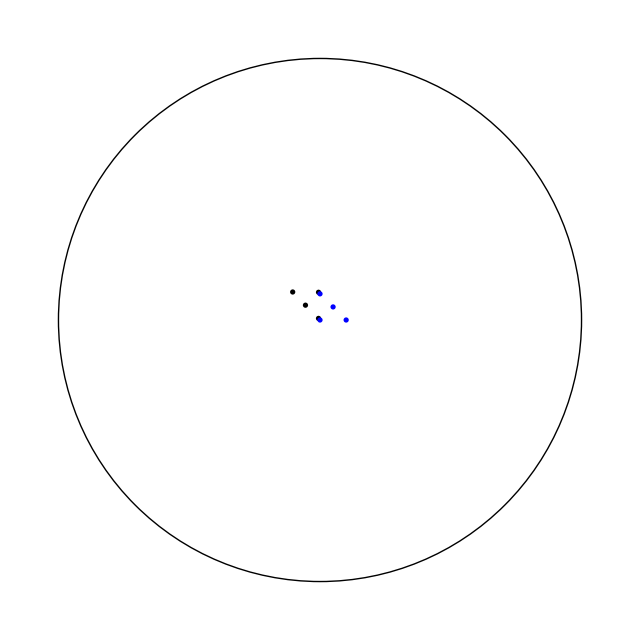

```mathematica
Graphics[{Circle[{0,0},1],Disk[Comp2Real[#∘BracketingBar[-0.0000+9.4169 I,0.9986+-0.0529 I]],.01]&/@{0,.1,.05I+.05,.1I},Blue,Disk[Comp2Real[#],.01]&/@{0,.1,.05I+.05,.1I}}]
```

```mathematica
{crowntransforms1,lens1,splanes1,totextrans1}={{BracketingBar[-2.1439+0.5123 I,0.7067+-0.7076 I],BracketingBar[-0.0509+1.5056 I,0.2866+-0.9581 I],BracketingBar[0.0124+2.0017 I,0.7377+-0.6751 I],BracketingBar[-8.3045+0.0000 I,-0.7474+-0.6644 I],BracketingBar[0.0793+-2.4792 I,0.9922+-0.1248 I],BracketingBar[0.0890+1.7688 I,0.9999+-0.0124 I],BracketingBar[1.9207+0.4430 I,0.9508+-0.3099 I],BracketingBar[0.6906+-1.6536 I,0.3153+-0.9490 I],BracketingBar[-0.7449+-1.5255 I,0.1665+-0.9860 I]},{2,2,2,2,2,2,2,2,2},{{{{0.7067,0.7076,0.0000,-0.0000},2},{{-1.8775,-1.1549,0.0000,1.9644},1}},{{{0.2866,0.9581,0.0000,-0.0000},2},{{-1.4570,0.3827,0.0000,1.1267},1}},{{{0.7377,0.6751,0.0000,-0.0000},2},{{-1.3423,1.4850,0.0000,1.7341},1}},{{{-0.7474,0.6644,0.0000,0.0000},2},{{6.2069,-5.5172,0.0000,8.2441},1}},{{{0.9922,0.1248,0.0000,0.0000},2},{{0.3880,-2.4500,0.0000,2.2700},1}},{{{0.9999,0.0124,0.0000,0.0000},2},{{0.0670,1.7698,0.0000,1.4617},1}},{{{0.9508,0.3099,0.0000,-0.0000},2},{{1.6889,1.0164,0.0000,1.6987},1}},{{{0.3153,0.9490,0.0000,0.0000},2},{{1.7870,0.1339,0.0000,1.4871},1}},{{{0.1665,0.9860,0.0000,-0.0000},2},{{1.3802,-0.9885,0.0000,1.3719},1}}},BracketingBar[8.3045+0.0000 I,-0.7474+-0.6644 I]};
```

```mathematica
mm2=-Graphics-;Graphics[{{Opacity[.9],Inset[mm2,Center,Center,2]},Circle[{0,0},1],Red,Disk[Comp2Real[0∘#],.012]&/@crowntransforms1}]
```

-Graphics-

```mathematica
{crowntransforms2,lens2,splanes2,totextrans2}={{BracketingBar[0.4244+1.4214 I,-0.8241+-0.5664 I],BracketingBar[-2.1439+0.5123 I,0.7067+-0.7076 I],BracketingBar[-0.0509+1.5056 I,0.2866+-0.9581 I],BracketingBar[0.0124+2.0017 I,0.7377+-0.6751 I],BracketingBar[-8.3045+0.0000 I,-0.7474+-0.6644 I],BracketingBar[0.0793+-2.4792 I,0.9922+-0.1248 I],BracketingBar[0.0890+1.7688 I,0.9999+-0.0124 I],BracketingBar[1.9207+0.4430 I,0.9508+-0.3099 I],BracketingBar[0.6906+-1.6536 I,0.3153+-0.9490 I],BracketingBar[-0.7449+-1.5255 I,0.1665+-0.9860 I]},{2,2,2,2,2,2,2,2,2,2},{{{{-0.8241,0.5664,0.0000,-0.0000},2},{{-1.1548,-0.9311,0.0000,1.0957},1}},{{{0.7067,0.7076,0.0000,-0.0000},2},{{-1.8775,-1.1549,0.0000,1.9644},1}},{{{0.2866,0.9581,0.0000,-0.0000},2},{{-1.4570,0.3827,0.0000,1.1267},1}},{{{0.7377,0.6751,0.0000,-0.0000},2},{{-1.3423,1.4850,0.0000,1.7341},1}},{{{-0.7474,0.6644,0.0000,0.0000},2},{{6.2069,-5.5172,0.0000,8.2441},1}},{{{0.9922,0.1248,0.0000,0.0000},2},{{0.3880,-2.4500,0.0000,2.2700},1}},{{{0.9999,0.0124,0.0000,0.0000},2},{{0.0670,1.7698,0.0000,1.4617},1}},{{{0.9508,0.3099,0.0000,-0.0000},2},{{1.6889,1.0164,0.0000,1.6987},1}},{{{0.3153,0.9490,0.0000,0.0000},2},{{1.7870,0.1339,0.0000,1.4871},1}},{{{0.1665,0.9860,0.0000,-0.0000},2},{{1.3802,-0.9885,0.0000,1.3719},1}}},BracketingBar[8.3045+0.0000 I,-0.7474+-0.6644 I]};
```

```mathematica
mm2=Import["/Users/strauss/Desktop/Screen Shot 2025-05-03 at 6.57.10 PM.png"];Graphics[{{Opacity[.9],Inset[mm2,Center,Center,2]},Circle[{0,0},1],Red,Disk[Comp2Real[0∘#],.012]&/@crowntransforms2,
Blue,Opacity[.6],
Disk[Comp2Real[0∘#],.009]&@|0.4244+1.4214 ⅈ,-0.8241-0.5664 ⅈ|

}]
```

-Graphics-

```mathematica
Complement[crowntransforms2,crowntransforms1]
```

```mathematica
Position[crowntransforms2,{|0.4244+1.4214 ⅈ,-0.8241-0.5664 ⅈ|}]
```

{}

```mathematica
ssplanes1={0.7067,0.7076,0.0000,-0.0000,2.0000,-1.8775,-1.1549,0.0000,1.9644,1.0000,0.2866,0.9581,0.0000,-0.0000,2.0000,-1.4570,0.3827,0.0000,1.1267,1.0000,0.7377,0.6751,0.0000,-0.0000,2.0000,-1.3423,1.4850,0.0000,1.7341,1.0000,-0.7474,0.6644,0.0000,0.0000,2.0000,6.2069,-5.5172,0.0000,8.2441,1.0000,0.9922,0.1248,0.0000,0.0000,2.0000,0.3880,-2.4500,0.0000,2.2700,1.0000,0.9999,0.0124,0.0000,0.0000,2.0000,0.0670,1.7698,0.0000,1.4617,1.0000,0.9508,0.3099,0.0000,-0.0000,2.0000,1.6889,1.0164,0.0000,1.6987,1.0000,0.3153,0.9490,0.0000,0.0000,2.0000,1.7870,0.1339,0.0000,1.4871,1.0000,0.1665,0.9860,0.0000,-0.0000,2.0000,1.3802,-0.9885,0.0000,1.3719,1.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000};
```

```mathematica
ssplanes2={-0.8241,0.5664,0.0000,-0.0000,2.0000,-1.1548,-0.9311,0.0000,1.0957,1.0000,0.7067,0.7076,0.0000,-0.0000,2.0000,-1.8775,-1.1549,0.0000,1.9644,1.0000,0.2866,0.9581,0.0000,-0.0000,2.0000,-1.4570,0.3827,0.0000,1.1267,1.0000,0.7377,0.6751,0.0000,-0.0000,2.0000,-1.3423,1.4850,0.0000,1.7341,1.0000,-0.7474,0.6644,0.0000,0.0000,2.0000,6.2069,-5.5172,0.0000,8.2441,1.0000,0.9922,0.1248,0.0000,0.0000,2.0000,0.3880,-2.4500,0.0000,2.2700,1.0000,0.9999,0.0124,0.0000,0.0000,2.0000,0.0670,1.7698,0.0000,1.4617,1.0000,0.9508,0.3099,0.0000,-0.0000,2.0000,1.6889,1.0164,0.0000,1.6987,1.0000,0.3153,0.9490,0.0000,0.0000,2.0000,1.7870,0.1339,0.0000,1.4871,1.0000,0.1665,0.9860,0.0000,-0.0000,2.0000,1.3802,-0.9885,0.0000,1.3719,1.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000,0.0000};
```

```mathematica
Take[ssplanes1,40]
```

{0.7067,0.7076,0.,0.,2.,-1.8775,-1.1549,0.,1.9644,1.,0.2866,0.9581,0.,0.,2.,-1.457,0.3827,0.,1.1267,1.,0.7377,0.6751,0.,0.,2.,-1.3423,1.485,0.,1.7341,1.,-0.7474,0.6644,0.,0.,2.,6.2069,-5.5172,0.,8.2441,1.}

```mathematica
Take[ssplanes2,{91,100}]
```

{0.1665,0.986,0.,0.,2.,1.3802,-0.9885,0.,1.3719,1.}

```mathematica
Show[%360,Graphics[{Circle[{0,0},1],(trans=#;Disk[Comp2Real[#∘trans],.01]&/@{0,.1,.05I+.05,.1I})&/@crowntransforms2,Blue}]]
```

-Graphics-

```mathematica
{crowntransforms1,lens1,splanes1,totextrans1}={{BracketingBar[-1.9069+0.4358 I,0.6969+-0.7171 I],BracketingBar[-0.1132+1.4396 I,0.2022+-0.9793 I],BracketingBar[-0.0768+1.9484 I,0.6262+-0.7797 I],BracketingBar[-8.0111+-0.0000 I,-0.2294+-0.9733 I],BracketingBar[-0.0313+2.3038 I,-0.9998+-0.0219 I],BracketingBar[0.0117+1.8610 I,0.9906+-0.1371 I],BracketingBar[2.1643+0.5152 I,0.9504+-0.3109 I],BracketingBar[0.7293+-1.8095 I,0.3768+-0.9263 I],BracketingBar[-0.8141+-1.5359 I,0.2788+-0.9603 I],BracketingBar[1.2366+0.5071 I,0.9100+-0.4147 I]},{2,2,2,2,2,2,2,2,2,2},{{{{0.6969,0.7171,0.0000,-0.0000},2},{{-1.6415,-1.0637,0.0000,1.6811},1}},{{{0.2022,0.9793,0.0000,0.0000},2},{{-1.4327,0.1802,0.0000,1.0417},1}},{{{0.6262,0.7797,0.0000,-0.0000},2},{{-1.5672,1.1602,0.0000,1.6739},1}},{{{-0.2294,0.9733,0.0000,0.0000},2},{{1.8375,-7.7975,0.0000,7.9484},1}},{{{-0.9998,0.0219,0.0000,0.0000},2},{{-0.0193,-2.3039,0.0000,2.0757},1}},{{{0.9906,0.1371,0.0000,-0.0000},2},{{-0.2436,1.8450,0.0000,1.5695},1}},{{{0.9504,0.3109,0.0000,-0.0000},2},{{1.8969,1.1626,0.0000,1.9874},1}},{{{0.3768,0.9263,0.0000,0.0000},2},{{1.9510,-0.0064,0.0000,1.6752},1}},{{{0.2788,0.9603,0.0000,0.0000},2},{{1.2480,-1.2100,0.0000,1.4219},1}},{{{0.9100,0.4147,0.0000,0.0000},2},{{0.9150,0.9743,0.0000,0.8868},1}}},BracketingBar[8.0111+-0.0000 I,-0.2294+-0.9733 I]};
```